```mathematica
val[s_,n_,i_]:=IntegerDigits[s,2,n][[i]]
```

```mathematica
Mask[n_,i_]:=Table[If[val[x,n,i]==val[y,n,i],val[y,n,i]-.5,0],{x,0,2^n-1},{y,0,2^n-1}]
```

{{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,1,0,0},{0,1,0,1},{0,1,1,0},{0,1,1,1},{1,0,0,0},{1,0,0,1},{1,0,1,0},{1,0,1,1},{1,1,0,0},{1,1,0,1},{1,1,1,0},{1,1,1,1},{0,0,0,0}}

```mathematica
n = 4;

collabels=ticks = Table[IntegerDigits[i,2,n],{i,0,2^n-1}];
rowlabels=ticks = Table[IntegerDigits[i,2,n],{i,0,2^n-1}];
rowticks=Thread[{Range[2^n],rowlabels}];
colticks=Thread[{Range[2^n],collabels}];
MatrixPlot[Mask[n,2],Mesh->All,FrameTicks->{rowticks,colticks}]//Dynamic
```

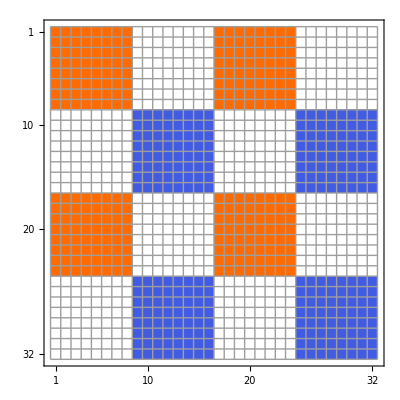

```mathematica
n = 5;
i=2;
MatrixPlot[Table[BitAnd[(2^n-1)-x,2^(n-i)]*BitAnd[(2^n-1)-y,2^(n-i)],{x,0,2^n-1},{y,0,2^n-1}]-Table[BitAnd[x,2^(n-i)]*BitAnd[y,2^(n-i)],{x,0,2^n-1},{y,0,2^n-1}],Mesh->All]
```

```mathematica
CreateMask[n_,i_]:=Table[BitAnd[(2^n-1)-x,2^(n-i)]*BitAnd[(2^n-1)-y,2^(n-i)],{x,0,2^n-1},{y,0,2^n-1}]-Table[BitAnd[x,2^(n-i)]*BitAnd[y,2^(n-i)],{x,0,2^n-1},{y,0,2^n-1}]
```

```mathematica
CreateMask[10,1]//MatrixPlot
```

-Graphics-

```mathematica
Table[BitAnd[(2^n-1)-x,2^(n-i)],{x,1,2^n-1}]
```

{4,4,4,0,0,0,0,4,4,4,4,0,0,0,0}

```mathematica
Table[{{IntegerDigits[(2^n-1)-x,2,4],IntegerDigits[2^(n-i),2,4]} , BitAnd[(2^n-1)-x,2^(n-i)]},{x,1,2^n-1}]//MatrixForm
```

({{1,1,1,0},{0,1,0,0}} | 4
{{1,1,0,1},{0,1,0,0}} | 4
{{1,1,0,0},{0,1,0,0}} | 4
{{1,0,1,1},{0,1,0,0}} | 0
{{1,0,1,0},{0,1,0,0}} | 0
{{1,0,0,1},{0,1,0,0}} | 0
{{1,0,0,0},{0,1,0,0}} | 0
{{0,1,1,1},{0,1,0,0}} | 4
{{0,1,1,0},{0,1,0,0}} | 4
{{0,1,0,1},{0,1,0,0}} | 4
{{0,1,0,0},{0,1,0,0}} | 4
{{0,0,1,1},{0,1,0,0}} | 0
{{0,0,1,0},{0,1,0,0}} | 0
{{0,0,0,1},{0,1,0,0}} | 0
{{0,0,0,0},{0,1,0,0}} | 0)

```mathematica
Not[5]
```

!5

```mathematica
~5
```